```mathematica
A[r_,theta_]:=(
a=r*Sin[(Pi-theta)/2]/Sin[theta/2];
b=r*Sin[theta/2]/Sin[(Pi-theta)/2];
(a+b)*r/2
)
A[r,2*Pi/k]
```

1/2 r (r Csc[1/2 (π-(2 π)/k)] Sin[π/k]+r Csc[π/k] Sin[1/2 (π-(2 π)/k)])

```mathematica
B[l_,r_,theta_]:=(
s=r*Sin[Pi/2-theta]/Sin[3*theta/2];
t=l*Sin[(Pi-theta)/2]/Sin[3*theta/2];
q=t*Sin[theta]/Sin[theta/2]-s;
h=q*Sin[Pi/2-theta];
y=q*Sin[3*theta/2]/Sin[(Pi-theta)/2];
(1/2)*y*h
)
B[l,r,2*Pi/k]
```

1/2 Cos[(2 π)/k] Csc[1/2 (π-(2 π)/k)] Sin[(3 π)/k] (-r Cos[(2 π)/k] Csc[(3 π)/k]+l Csc[π/k] Csc[(3 π)/k] Sin[(2 π)/k] Sin[1/2 (π-(2 π)/k)])^2

```mathematica
f[l_,theta_]:=(
Integrate[(1/l)*E^(-A[r,theta]-B[l,r,theta]), {r,0,l}]
)
f[l,2*Pi/k]
```

1/(l (4+11 Cos[(2 π)/k]+Cos[(6 π)/k]))ⅇ^(-(8 l^2 Cos[π/k]^2 Cos[(2 π)/k] Cot[π/k])/(4+11 Cos[(2 π)/k]+Cos[(6 π)/k])) √(π/2) (Erf[(√2 l (Cos[π/k]+Cos[(3 π)/k])^2)/(√(18 Sin[(2 π)/k]+18 Sin[(4 π)/k]+11 Sin[(6 π)/k]+Sin[(8 π)/k]+Sin[(10 π)/k]))]+Erf[(2 √2 l (2 Cos[(2 π)/k]+Sin[(2 π)/k]^2))/(√(18 Sin[(2 π)/k]+18 Sin[(4 π)/k]+11 Sin[(6 π)/k]+Sin[(8 π)/k]+Sin[(10 π)/k]))]) √(18 Sin[(2 π)/k]+18 Sin[(4 π)/k]+11 Sin[(6 π)/k]+Sin[(8 π)/k]+Sin[(10 π)/k])

```mathematica
Q[x_,theta_] := 1-Exp[-x^2*Sin[(Pi-theta)/2]/Sin[theta/2]]
Q[x,theta]
```

1-ⅇ^(-x^2 Csc[theta/2] Sin[(π-theta)/2])

```mathematica
p:=Function[{x,theta},D[Q[x,theta],x]]
p[x,alpha]
```

2 ⅇ^(-x^2 Csc[alpha/2] Sin[1/2 (-alpha+π)]) x Csc[alpha/2] Sin[1/2 (-alpha+π)]

```mathematica
Integrate[p[l,2*Pi/k]*f[l,2*Pi/k],{l,0,Infinity}]
```

ConditionalExpression[(2 (ArcTan[(2 (Cos[π/k]+Cos[(3 π)/k])^2)/(√(((27 Cos[π/k]+17 Cos[(3 π)/k]+3 Cos[(5 π)/k]+Cos[(7 π)/k]) Csc[π/k])/(4+11 Cos[(2 π)/k]+Cos[(6 π)/k])) √(18 Sin[(2 π)/k]+18 Sin[(4 π)/k]+11 Sin[(6 π)/k]+Sin[(8 π)/k]+Sin[(10 π)/k]))]+ArcTan[(4 (2 Cos[(2 π)/k]+Sin[(2 π)/k]^2))/(√(((27 Cos[π/k]+17 Cos[(3 π)/k]+3 Cos[(5 π)/k]+Cos[(7 π)/k]) Csc[π/k])/(4+11 Cos[(2 π)/k]+Cos[(6 π)/k])) √(18 Sin[(2 π)/k]+18 Sin[(4 π)/k]+11 Sin[(6 π)/k]+Sin[(8 π)/k]+Sin[(10 π)/k]))]) Cot[π/k] √(18 Sin[(2 π)/k]+18 Sin[(4 π)/k]+11 Sin[(6 π)/k]+Sin[(8 π)/k]+Sin[(10 π)/k]))/((4+11 Cos[(2 π)/k]+Cos[(6 π)/k]) √(((27 Cos[π/k]+17 Cos[(3 π)/k]+3 Cos[(5 π)/k]+Cos[(7 π)/k]) Csc[π/k])/(4+11 Cos[(2 π)/k]+Cos[(6 π)/k]))),Re[(2 Cos[(2 π)/k]+Sin[(2 π)/k]^2)/(√(18 Sin[(2 π)/k]+18 Sin[(4 π)/k]+11 Sin[(6 π)/k]+Sin[(8 π)/k]+Sin[(10 π)/k]))]>0&&Re[(Cos[π/k]+Cos[(3 π)/k])^2/(√(18 Sin[(2 π)/k]+18 Sin[(4 π)/k]+11 Sin[(6 π)/k]+Sin[(8 π)/k]+Sin[(10 π)/k]))]>0]

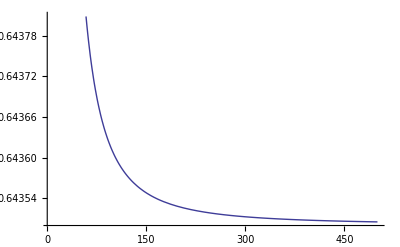

```mathematica
Plot[Out[-1],{k,5,500}]
```

```mathematica
Limit[Out[-2],k->Infinity]
```

2 ArcTan[1/3]

```mathematica
N[Out[-1],10]
```

0.6435011088

```mathematica
N[Out[-4]/.k->{5,7,9,11,13,15,17,19},10]
```

ConditionalExpression[{0.7016846301,0.6677804005,0.6574093213,0.6525989555,0.649936598,0.648300274,0.6472202096,0.6464690223},{0.3380719452,0.3141646314,0.3122009385,0.3202266053,0.3325506162,0.3467489425,0.3617134574,0.3769036388}>0&&{0.05551108563,0.2133996677,0.3326557494,0.4226022265,0.4948420394,0.5558278929,0.6091735856,0.6570293859}>0]

```mathematica
N[k*(2-Out[-5])/.k->{5,7,9,11,13,15,17,19},10]
```

ConditionalExpression[{6.49157685,9.325537196,12.08331611,14.82141149,17.55082423,20.27549589,22.99725644,25.71708858},{0.3380719452,0.3141646314,0.3122009385,0.3202266053,0.3325506162,0.3467489425,0.3617134574,0.3769036388}>0&&{0.05551108563,0.2133996677,0.3326557494,0.4226022265,0.4948420394,0.5558278929,0.6091735856,0.6570293859}>0]